```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

# Free energy For SRO that matches Experimental predictions

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Here I will start with a Function in R^2 which which has this 1 well 1 touching point structure.
We will rotated this function about the z axis by some angle. We will then change the control points along the x axis by specifying a function that describes the z coordinate of the control points.
The sequence of Things that we will do is
1. Determine the control points that should match varphi(x,y)(=h(x)g(y))
2. Get the control points of the Rotated function (by 45 degree )and plot it
3. Define a function Ctrlz[x] which will be used to specify the control points.
*)
```

## (*1.Determine the control points that should match varphi(x,y)(=h(x)g(y)) *)

```mathematica
(*1a. Passing a BSpline curve through points in R^2*)
```

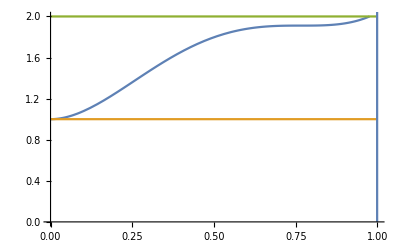

{{0.,1.},{0.166429,1.11265},{0.305959,1.53682},{0.623009,1.99637},{0.887246,1.85038},{1.,2.03711}}

-Graphics-

```mathematica
(*We want a BSpline surface that passes through the desired points. We are interested in the BSpline interpolation of the funciton
f(x,y)=h(x)g(y)
 where
h(x)=((l*x)^4/4-a/3*(l*x)^3+(b+1/4)*a^2/2*(l*x)^2)/((l*1)^4/4-a/3*(l*1)^3+(b+1/4)*a^2/2*(l*1)^2)+1
(*THE FOLLOWING FUNCTION HAS 1 WELL AND 1 TOUCHING POINT. THIS CAN BE FOUND IN "QUARTICENERGY_1WELL.NB"*)
g(y)=1+y^2
We interpolate them separately by picking uniformly spaced points on them.
*)
l=7.5;(*This is to scale the x axis*)
a=11.5;
b=0.0;
M=0.01;
N1=5;
(*h1[x_]:=(1+x^2)*)
h0[x_]:=M*((l*x)^4/4-a/3*(l*x)^3+(b+1/4)*a^2/2*(l*x)^2)+1 
h1[x_]:=h0[x]
Show[Plot[{h1[x],1,2},{x,0,1},PlotRange->{0,2}],ContourPlot[x==0.999,{x,0,1},{y,0,10}]]
testData=Table[{i/N1,h1[i/N1]},{i,0,N1}];
parametrizeCurve[pts_/;MatrixQ[pts,NumericQ],a:(_?NumericQ):1/2]:=FoldList[Plus,0,Normalize[(Norm/@Differences[pts])^a,Total]]
tvals=parametrizeCurve[testData];
m=3;(*degree of the B-spline*)(*knots for interpolating B-spline*)
ConstantArray[0,m+1];
ArrayPad[tvals,-1];(*gets rid of one term on either side*)
MovingAverage[ArrayPad[tvals,-1],m];(*Moving average is when you compute the average of m consecutive points.*)
ConstantArray[1,m+1];
knots=Join[ConstantArray[0,m+1],MovingAverage[ArrayPad[tvals,-1],m],ConstantArray[1,m+1]];
(*basis function matrix*)
bas=Table[BSplineBasis[{m,knots},j-1,tvals[[i]]]//N,{i,Length[testData]},{j,Length[testData]}];
ctrlpts=LinearSolve[bas,testData]
{Graphics[{{ColorData[1,1],BSplineCurve[ctrlpts,SplineDegree->m,SplineKnots->knots]},{Directive[Green,AbsolutePointSize[6]],Point[testData]}},Frame->True],ParametricPlot[BSplineFunction[ctrlpts,SplineDegree->m,SplineKnots->knots][t]//Evaluate,{t,0,1},Axes->None,Epilog->{Directive[Green,AbsolutePointSize[6]],Point[testData]},Frame->True]}//GraphicsRow
```

```mathematica
(*1b. Passing a surface through Points in R^3.*)
```

```mathematica
(*We got the values for the Control points by from running the above for h(x) and g(y) separately.*)
(*Data for N1=7*)
Ctrlx={{0.,1.0969000000000002},{0.11277115015472801,0.904304339919332},{0.25478585286514444,1.1352009766109796},{0.41706709074618153,1.394642642541528},{0.554159059496832,1.5560620520330772},{0.7638516753866764,1.616859938741391},{0.9231096669382652,1.5658364748601243},{1.,1.7209000000000017}};
Ctrly={{0.,1.},{0.09913916384952173,0.9995558743327182},{0.24930285544736355,1.0469199263075883},{0.43684069277542564,1.1840171065536713},{0.5797743540440522,1.329348687494005},{0.7751071455411349,1.5837339936602406},{0.9111748816259047,1.8226673819108743},{1.0000000000000002,2.0000000000000004}};
Ctrl=Table[{Ctrlx[[i]][[1]],Ctrly[[j]][[1]],Ctrlx[[i]][[2]]*Ctrly[[j]][[2]]},{i,1,Length[Ctrlx]},{j,1,Length[Ctrly]}];
Show[Graphics3D[{PointSize[Medium],Red,Map[Point,Ctrl],Gray,Line[Ctrl],Line[Transpose[Ctrl]]}],Graphics3D[BSplineSurface[Ctrl]],Plot3D[h1[x]*g1[y],{x,0,1},{y,0,1}]]
```

-Graphics3D-

```mathematica
(*2. Get the control points of the Rotated function (by 45 degree )and plot it.*)
```

```mathematica
(*Check the Mathematica Code "SurfaceFittingBSplines.nb" for Details.*)
```

```mathematica
α=0.2;
β=Sqrt[1-α^2];
lx=3.8;
ly=1.0;
Mx=0.3;
h3[x_,a_,b_]:=Mx*((lx*x)^4/4-a/3*(lx*x)^3+(b+1/4)*a^2/2*(lx*x)^2)+1 
g3[y_]:=(1+(ly*y)^2)
Manipulate[Plot3D[h3[α*(x)+β*y,a,0]*g3[-β*(x)+α*y],{x,0,1},{y,0,1},AxesLabel->Automatic,PlotRange->{0,2}],{{a,3.5},0,10}]
(*The values of a,b,lx,ly were decided using the manipulate above*)
a=3.5;
b=0.0;
S[x_,y_]:=h3[α*x+β*y,a,b]*g3[-β*x+α*y]
Nx=5;
Ny=5;
testData=Table[{i/Nx,j/Ny,S[i/Nx,j/Ny]},{i,0,Nx},{j,0,Ny}];
parametrizeCurve[pts_/;MatrixQ[pts,NumericQ],a:(_?NumericQ):1/2]:=FoldList[Plus,0,Normalize[(Norm/@Differences[pts])^a,Total]]
tvalsTempx=Range[Nx+1];
tvalsTempy=Range[Ny+1];
tvalsx=Range[Nx+1];
tvalsy=Range[Ny+1];
For[j=1,j<=Ny+1,j++,tvalsTempx[[j]]=parametrizeCurve[Table[{i/Nx,j/Ny,S[i/Nx,j/Ny]},{i,0,Nx}]]]
tvalsx=Mean[tvalsTempx]//N;
For[i=1,i<=Nx+1,i++,tvalsTempy[[i]]=parametrizeCurve[Table[{i/Nx,j/Ny,S[i/Nx,j/Ny]},{j,0,Ny}]]]
tvalsy=Mean[tvalsTempy]//N;
mx=3;(*degree of the B-spline*)(*knots for interpolating B-spline*)
ConstantArray[0,mx+1];
ArrayPad[tvalsx,-1];(*gets rid of one term on either side*)
MovingAverage[ArrayPad[tvalsx,-1],mx];(*Moving average is when you compute the average of m consecutive points.*)
ConstantArray[1,mx+1];
knotsx=Join[ConstantArray[0,mx+1],MovingAverage[ArrayPad[tvalsx,-1],mx],ConstantArray[1,mx+1]]//N;
my=3;(*degree of the B-spline*)(*knots for interpolating B-spline*)
ConstantArray[0,my+1];
ArrayPad[tvalsy,-1];(*gets rid of one term on either side*)
MovingAverage[ArrayPad[tvalsy,-1],my];(*Moving average is when you compute the average of m consecutive points.*)
ConstantArray[1,my+1];
knotsy=Join[ConstantArray[0,my+1],MovingAverage[ArrayPad[tvalsy,-1],my],ConstantArray[1,my+1]]//N;
ctrlptsx=Range[Nx+1];
For[k=0,k<=Nx,k++,
bas=Table[BSplineBasis[{mx,knotsx},j-1,tvalsx[[i]]],{i,Length[Table[{k/Nx,l/Ny,S[k/Nx,l/Ny]},{l,0,Ny}]]},{j,Length[Table[{k/Nx,l/Ny,S[k/Nx,l/Ny]},{l,0,Ny}]]}];
ctrlptsx[[k+1]]=LinearSolve[bas,Table[{k/Nx,l/Ny,S[k/Nx,l/Ny]},{l,0,Ny}]]
]
ctrlpts=Range[Ny+1];
For[l=1,l<=Ny+1,l++,
bas=Table[BSplineBasis[{my,knotsy},j-1,tvalsy[[i]]],{i,Length[ctrlptsx[[All,l,All]]]},{j,Length[ctrlptsx[[All,l,All]]]}];
ctrlpts[[l]]=LinearSolve[bas,ctrlptsx[[All,l,All]]]
]
Show[Graphics3D[BSplineSurface[ctrlpts,SplineDegree->{mx,my},SplineKnots->{knotsx,knotsy}],PlotRange->{0,20},PlotRegion->{{0,1},{0,1}},BoxRatios->{1, 1, 1}],ListPointPlot3D[testData]]
```

-Graphics3D-

```mathematica
Dimensions[ctrlpts]
ctrlpts
```

{6,6,3}

{{{0.,0.,1.},{0.111988,0.,0.975607},{0.44367,0.,1.18133},{0.870785,0.,1.86485},{0.841706,0.,1.88362},{1.,0.,2.22796}},{{0.,0.164211,1.10554},{0.111988,0.164211,1.11446},{0.44367,0.164211,1.38344},{0.870785,0.164211,2.12395},{0.841706,0.164211,2.12228},{1.,0.164211,2.47334}},{{0.,0.384521,1.28989},{0.111988,0.384521,1.23657},{0.44367,0.384521,1.32935},{0.870785,0.384521,1.77174},{0.841706,0.384521,1.76825},{1.,0.384521,1.99642}},{{0.,0.718914,1.18784},{0.111988,0.718914,1.128},{0.44367,0.718914,1.30934},{0.870785,0.718914,2.32508},{0.841706,0.718914,2.53388},{1.,0.718914,3.19808}},{{0.,0.889239,1.95319},{0.111988,0.889239,1.9949},{0.44367,0.889239,2.79386},{0.870785,0.889239,5.73855},{0.841706,0.889239,6.28358},{1.,0.889239,8.08885}},{{0.,1.,3.86465},{0.111988,1.,3.96934},{0.44367,1.,5.40946},{0.870785,1.,10.5268},{0.841706,1.,11.399},{1.,1.,14.4621}}}

## (*3. Manipulate Multiple Control Points *)

```mathematica
(*Here we manipulate multiple control points. We do so by introducing a function. form which we could take z values*)
(*Here we want to manipulate The control points to math the following function
 f(x,y)=h(x)g(y).
We specify a variable zz, that will be the z value of the control points along the xaxis.
This part of the code should just manipulate the control point along the x axis.
*)
zz={{0.,1.0000000000000002},{0.1664291714565248,1.1126494638781057},{0.30595889704008056,1.5368159975632485},{0.6230091752149005,1.996367493102534},{0.8872458175561295,1.8503753136058976},{1.0000000000000002,2.0371093750000027}};
zz=zz[[All,2]];(*ctrlpts[[All,1,3]];*)
Ctrl=Table[If[j==1,{ctrlpts[[i,j,1]],ctrlpts[[i,j,2]],zz[[i]]},{ctrlpts[[i,j,1]],ctrlpts[[i,j,2]],ctrlpts[[i,j,3]]}],{i,1,Nx+1},{j,1,Ny+1}];(*Modifying the values near the x axis*)
(*Ctrl=ctrlpts;*)(*This is to test.*)
(*Ctrl-ctrlpts*)
Lx=1;
Ly=Lx;
Lz=Lx;
x1=0;xN=Lx;Δx=0.1;
y1=0;yN=Ly;Δy=0.1;
bartab=Join@@Table[{i,j},{i,x1,xN,Δx},{j,y1,yN,Δy}];
Sx[u_,v_]:=Sum[Lz*Ctrl[[i,j,1]]*BSplineBasis[{mx,knotsx},i-1,u/Lx]*BSplineBasis[{my,knotsy},j-1,v/Ly],{i,Nx+1},{j,Ny+1}]
Sy[u_,v_]:=Sum[Lz*Ctrl[[i,j,2]]*BSplineBasis[{mx,knotsx},i-1,u/Lx]*BSplineBasis[{my,knotsy},j-1,v/Ly],{i,Nx+1},{j,Ny+1}]
Sz[u_,v_]:=Sum[Lz*Ctrl[[i,j,3]]*BSplineBasis[{mx,knotsx},i-1,u/Lx]*BSplineBasis[{my,knotsy},j-1,v/Ly],{i,Nx+1},{j,Ny+1}]
s=1;
ParametricPlot3D[{Sx[u,v],Sy[u,v],Sz[u,v]},{u,0,1},{v,0,1},PlotRange->{{0,1},{0,1},{0,4}}]
Soln=NMinimize[{Sz[u,v]-s*Sx[u,v],Sy[u,v]>=0,0<=u<=Lx,0<=v<=Ly},{u,v},Method->{"NelderMead","InitialPoints"->bartab}];
(*Show[Graphics3D[BSplineSurface[Ctrl]],Plot3D[{s*u1+Soln[[1]]},{u1,0,1},{v1,0,1}]]*)
(*Plot3D[{Sz[u1,v1],s*Sx[u1,v1]+Soln[[1]]},{u1,0,Lx},{v1,0,Ly},PlotRange->{0,20},AxesLabel->Automatic]*)
Show[ParametricPlot3D[{{Sx[u1,v1],Sy[u1,v1],s*Sx[u1,v1]+Soln[[1]]},{Sx[u1,v1],Sy[u1,v1],Sz[u1,v1]}},{u1,0,1},{v1,0,1},PlotRange->{{0,1},{0,1},{0,4}},AxesLabel->Automatic],Graphics3D[{Red,PointSize[0.1],Point[{Sx[u/.Soln[[2]],v/.Soln[[2]]],Sy[u/.Soln[[2]],v/.Soln[[2]]],Sz[u/.Soln[[2]],v/.Soln[[2]]]}]},BoxRatios->{1, 1, 0.2}]]
Soln[[2]]
```

-Graphics3D-

-Graphics3D-

{u→0.,v→0.217672}

```mathematica
Dimensions[Ctrl];
ArrayReshape[Ctrl,{Dimensions[Ctrl][[1]]*Dimensions[Ctrl][[2]],Dimensions[Ctrl][[3]]}];
Show[Graphics3D[{Red,PointSize[.05],Point[ArrayReshape[Ctrl,{Dimensions[Ctrl][[1]]*Dimensions[Ctrl][[2]],Dimensions[Ctrl][[3]]}]]},BoxRatios->{2, 2,2},PlotRange->{{0,1},{0,1},{1,15}},Axes->True,LabelStyle->Directive[Bold,Medium],AxesLabel->{"x","y","z"}],Graphics3D[{Blue,PointSize[.05],Point[ArrayReshape[ctrlpts,{Dimensions[ctrlpts][[1]]*Dimensions[ctrlpts][[2]],Dimensions[ctrlpts][[3]]}]]},BoxRatios->{2, 2, 2},PlotRange->{{0,1},{0,1},{1,15}},Axes->True,LabelStyle->Directive[Bold,Medium],AxesLabel->{"x","y","z"}]
]
```

-Graphics3D-

### (*Last. Testing out the different shapes of the Touching points*)

```mathematica
hh1[x_,a1_,b1_,l1_,M1_]:=M1*((l1*x)^4/4-a1/3*(l1*x)^3+(b1+1/4)*a1^2/2*(l1*x)^2)+1 
hh2[x_,a2_,b2_,l2_,M2_]:=M2*((l2*x)^4/4-a2/3*(l2*x)^3+(b2+1/4)*a2^2/2*(l2*x)^2)+1 
Manipulate[Show[Plot[{hh1[x,a1,b1,l1,M1],hh2[x-0.1,a2,b2,l2,M2],1,4},{x,0,1},PlotRange->{0,4},PlotLegends->{"hh1","hh2"}],ContourPlot[x==0.999,{x,0,1},{y,0,10}]],{{a1,11.5},0,20},{b1,0,1/12},{{l1,8.5},0.01,10},{{M1,0.01},0,1},{{a2,3.5},0,20},{b2,0,1/12},{{l2,3.8},0.01,50},{{M2,0.3},0,1}]
```

```mathematica
cylinderPlot3D[f_,{rMin_,rMax_},{tMin_,tMax_},opts___]:=ParametricPlot3D[{r Cos[t],r Sin[t],f[r,t]},{r,rMin,rMax},{t,tMin,tMax},opts];
aa[t_]:=7.5+4*Cos[4*t+Pi/12]
bb[t_]:=-1/36*Sin[4*t+Pi/12]
lr[t_]=7.25+1.25*Cos[4*t+Pi/12];
Mr[t_]=0.205-0.195*Cos[4*t+Pi/12];
gg[r_,t_]:=(lr[t]*r)^4/4-aa[t]/3*(lr[t]*r)^3+(bb[t]+1/4)*aa[t]^2/2*(lr[t]*r)^2
ff[r_,t_]:=gg[r,t]*Mr[t]/Mr[Pi/4]+1;
Manipulate[{aa[Pi*t],bb[Pi*t],Plot[{ff[r,Pi*t]},{r,0,1},PlotRange->{0,14},PlotLegends->{"ff(r)"}]},{t,0,2}]
RevolutionPlot3D[ff[r,t],{r,1,0},{t,2*Pi,0},PlotRange->{{-1,1},{-1,1},{1,10}}]
RevolutionPlot3D[r*Cos[t]+1,{r,1,0},{t,2*Pi,0},PlotRange->{{-1,1},{-1,1},{1,10}}]
```

-Graphics3D-

-Graphics3D-